## Installing, Loading, Uninstalling Paclet

## Installing a paclet

```mathematica
PacletInstall["C:\Users\Dinosaur\Downloads\ECGrav-1.0.0.paclet",ForceVersionInstall->True]
```

PacletObject[…]

## Loading the package in a paclet

```mathematica
(*Quit[];*)
```

```mathematica
Needs["ECGrav`"]
ParallelNeeds["ECGrav`"]
```

## Uninstalling a paclet

```mathematica
PacletFind["ECGrav"]
(*PacletFind[<|"Context"->"ECGrav`"|>]*)
```

{PacletObject[…]}

```mathematica
PacletUninstall[First@PacletFind[<|"Context"->"ECGrav`"|>]]
```

# PureComplexes Examples

## Helper Functions

## General

### Basic Simplicial Complex Constructions

PureComplexQ/PureGraphQ

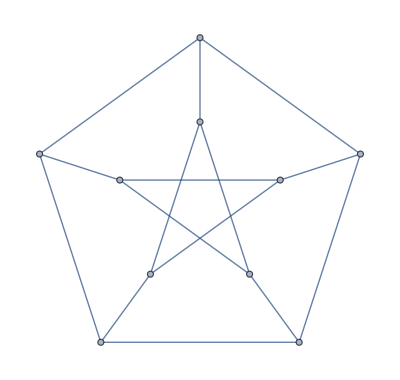
```mathematica
PureComplexQ[-Graphics-,5]
PureComplexQ[fstLst]
PureGraphQ[-Graphics-]
```

PureComplexQ::argerr: Input should be a list of lists (i.e., list of facets)

$Failed

True

True

FacetLabeledVertexListFromComplex

FacetLabeledVertexListFromComplex::argerr: -- Message text not found -- () (5)

$Failed

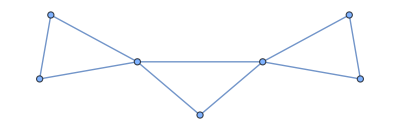

{{1,3},{2,3},{1},{1},{2},{2},{3}}

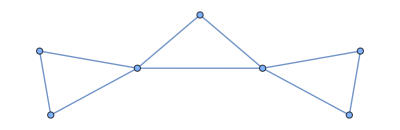

```mathematica
FacetLabeledVertexListFromComplex[-Graphics-,5]
GraphFromCliques[fstLst]
FacetLabeledVertexListFromComplex[fstLst]
GraphFromCliques[ComplexFromFacetLabeledVertexList[%]]
```

ComplexFromFacetLabeledVertexList

ComplexFromFacetLabeledVertexList::argerr: Input should be a list of lists 
	(i.e., list of vertices given as a list of facets they belong to)

$Failed

{{1,2,6},{3,6},{4,5},{6,7}}

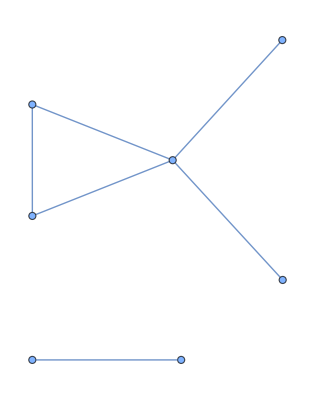

```mathematica
ComplexFromFacetLabeledVertexList[-Graphics-,5]
ComplexFromFacetLabeledVertexList[{{1},{1},{2},{3},{3},{1,2,4},{4}}]
GraphFromCliques[%]
```

CliquesFromFacetIncidence

```mathematica
CliquesFromFacetIncidence[-Graphics-,5]
CliquesFromFacetIncidence[FacetIncidenceMatrix[{{1,2,3},{2,3,4}}]]
```

CliquesFromFacetIncidence::argerr: Input should be a {0,1} matrix (the facet-incidence)

$Failed

{{1,2,3},{2,3,4}}

GraphFromFacetIncidence

GraphFromFacetIncidence::argerr: Input should be a {0,1} matrix (the facet-incidence)

$Failed

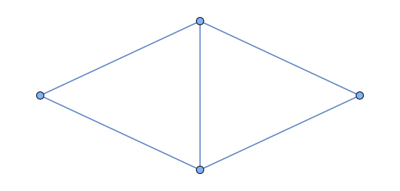

```mathematica
GraphFromFacetIncidence[-Graphics-,5]
GraphFromFacetIncidence[FacetIncidenceMatrix[{{1,2,3},{2,3,4}}]]
```

GraphFromCliques

```mathematica
GraphFromCliques[-Graphics-,5]
GraphFromCliques[{{1,2,3},{2,3,4}}]
```

GraphFromCliques::argerr: Input should be a list of lists (i.e., list of masimal cliques).

$Failed

-Graphics-

FacetAdjacencyMatrix

```mathematica
FacetAdjacencyMatrix[-Graphics-,5]
FacetAdjacencyMatrix[-Graphics-]//MatrixForm
FacetAdjacencyMatrix[{{1,2,3},{2,3,4}}]
```

FacetAdjacencyMatrix::argerr: Input should be a list of lists (i.e., list of facets) 
	or a graph object

$Failed

(2 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 2 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 1 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 2 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 2 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 2 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 2)

{{3,2},{2,3}}

FacetIncidenceMatrix

```mathematica
FacetIncidenceMatrix[-Graphics-,5]
FacetIncidenceMatrix[-Graphics-]//MatrixForm
FacetIncidenceMatrix[{{1,2,3},{2,3,4}}]
```

FacetIncidenceMatrix::argerr: Input should be a list of lists (i.e., list of facets) 
	or a graph object

$Failed

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1)

{{1,1,1,0},{0,1,1,1}}

```mathematica
FacetAdjacencyMatrix[]
```

```mathematica
GetComplexFromInt[5,2,4]
```

{{0,1},{0,2},{0,3},{1,3}}

```mathematica
GetIntFromComplex[{{0,1},{0,2},{0,3},{1,3}}]
```

5

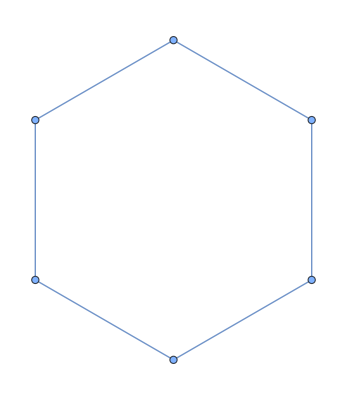
```mathematica
{DSphereQ[#],DGraphQ[#],DBoundary[#],CountHoles[#]}&/@{-Graphics-,-Graphics-}
```

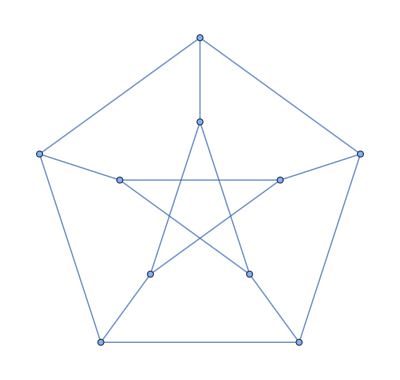
{{False,False,-Graphics-,{1,6}},{True,True,-Graphics-,{1,1}}}

```mathematica
{AvgKDim[#],SpectralDim[#,2],HausdorffDim[#,2]}&@-Graphics-
```

{1,3.16993,3.16993}

```mathematica
SpectralDim[-Graphics-,2]
```

3.16993

```mathematica
GVolume[-Graphics-,2,1]
```

9

```mathematica
AdjacencyGraph[Sph[Normal[AdjacencyMatrix[-Graphics-]],1,2]]
Bll[-Graphics-,1,2]
```

-Graphics-

-Graphics-

```mathematica
CliqueOrder[-Graphics-]
```

15

```mathematica
KVertexConnectedComponents
```

```mathematica
KpathConnectedComponents[FindClique[-Graphics-,∞,All],2]
```

{}

```mathematica
Max[Length/@{}]
```

-∞

```mathematica
FractionInLargestKPathComponent[-Graphics-,1]
```

1

```mathematica
{RmsPurity[#],EulerChi[#],EulerChi[FindClique[#,∞,All]],Branchedness[#],Branchedness[Normal[AdjacencyMatrix[#]]],FacetOrder[FindClique[#,∞,All]],CliqueOrder[#],FractionInLargestKPathComponent[#,1],FractionInLargestComponent[#],ConnectedComplexComponents[FindClique[#,∞,All]],KpathConnectedComponents[FindClique[#,∞,All],1]}&@-Graphics-
```

{0,-5,-5,2,2,15,15,1,1,{{{6,10},{9,10},{4,9},{8,9},{3,8},{7,8},{6,7},{5,10},{3,5},{2,7},{2,5},{2,4},{1,6},{1,4},{1,3}}},{{6,10,9,4,8,3,7,5,2,1}}}

```mathematica
KpathConnectedComponents[FindClique[-Graphics-,∞,All],1]
```

{{6,10,9,4,8,3,7,5,2,1}}

```mathematica
ConnectedComplexComponents[FindClique[-Graphics-,∞,All]]
```

{{{6,10},{9,10},{4,9},{8,9},{3,8},{7,8},{6,7},{5,10},{3,5},{2,7},{2,5},{2,4},{1,6},{1,4},{1,3}}}

```mathematica
KpathConnectedComponents[FindClique[-Graphics-,∞,All],2]
```

{}

### Spheres and Balls, Links and Stars

Sph and Bll

in case graph. graph = -Graphics-

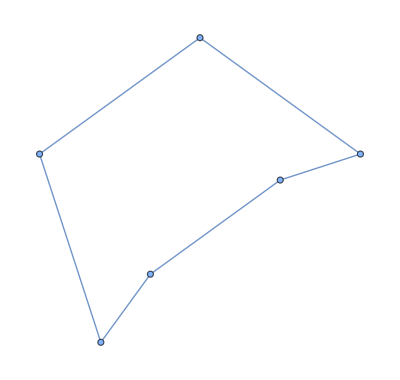

in case Amat. Amat = {{0,0,1,1,0,1,0,0,0,0},{0,0,0,1,1,0,1,0,0,0},{1,0,0,0,1,0,0,1,0,0},{1,1,0,0,0,0,0,0,1,0},{0,1,1,0,0,0,0,0,0,1},{1,0,0,0,0,0,1,0,0,1},{0,1,0,0,0,1,0,1,0,0},{0,0,1,0,0,0,1,0,1,0},{0,0,0,1,0,0,0,1,0,1},{0,0,0,0,1,1,0,0,1,0}}

{{0,1,1,0,0,0},{1,0,0,1,0,0},{1,0,0,0,0,1},{0,1,0,0,1,0},{0,0,0,1,0,1},{0,0,1,0,1,0}}

-Graphics-

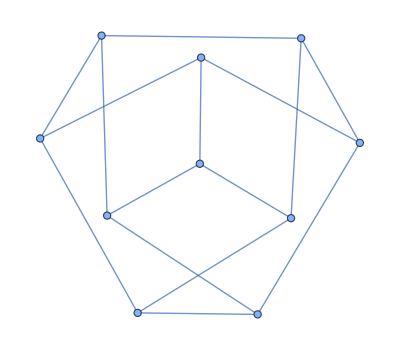

```mathematica
g=-Graphics-;
Sph[g,2,2]
Sph[Normal[AdjacencyMatrix[g]],2,2]


Bll[g,2,2]
AdjacencyGraph[Bll[Normal[AdjacencyMatrix[g]],2,5]]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

Lnk and Str

```mathematica
fstLst={{1,2,3},{4,5,6},{2,4,7}};

Lnk[fstLst,1]
Lnk[fstLst,{2}]

Str[fstLst,1]
Str[fstLst,{2}]
```

Lnk::argerr: A list of facets is expected at 
	position 1 a list at position 2.

$Failed

{{1,3},{4,7}}

Str::argerr: A list of facets is expected at 
	position 1 a list at position 2.

$Failed

{{1,2,3},{2,4,7}}

### Basic Graph Observables

Deg, AvgDeg, HyperDeg,GVolume, FacetDeg, KFaceDistance,CliqueOrder

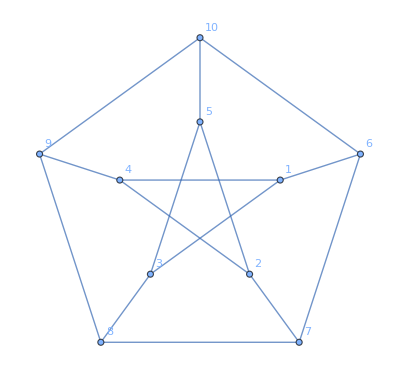
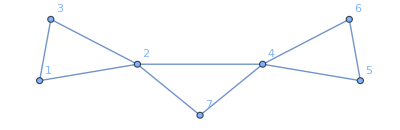

```mathematica
g=-Graphics-;
fstLst={{1,2,3},{4,5,6},{2,4,7}};
GraphPlot[#,VertexLabels->Automatic]&/@{g,GraphFromCliques[fstLst]}
```

```mathematica
{Deg[Normal[AdjacencyMatrix[#]],1],AvgDeg[#],HyperDeg[#,{1}],GVolume[#,1,1],CliqueOrder[#]}&/@{g}
```

{{3,3,3,3,15}}

```mathematica
KFaceDistance[#,{1,2},{5,6}]&/@{fstLst}
```

{∞}

```mathematica
FacetDeg[#,2]&@fstLst
```

2

KFaceDistanceMatrix, KpathConnectedComponents,ConnectedComplexComponents,FacetOrder

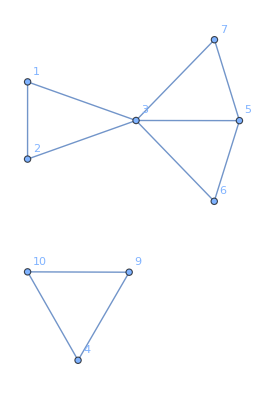
{-Graphics-,-Graphics-}

```mathematica
g=-Graphics-;
fstLst={{1,2,3},{3,5,6},{3,5,7},{4,9,10}};
GraphPlot[#,VertexLabels->Automatic]&/@{g,GraphFromCliques[fstLst]}
```

```mathematica
{KFaceDistanceMatrix[#,2]//MatrixForm,KpathConnectedComponents[#,2],ConnectedComplexComponents[#],FacetOrder[#]}&/@{fstLst}
```

{{(0 | 1 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 0 | 1 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
1 | 1 | 0 | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞
∞ | ∞ | ∞ | 0 | 1 | 1 | ∞ | ∞ | 1 | 1 | ∞
∞ | ∞ | ∞ | 1 | 0 | 2 | ∞ | ∞ | 1 | 2 | ∞
∞ | ∞ | ∞ | 1 | 2 | 0 | ∞ | ∞ | 2 | 1 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1 | ∞ | ∞ | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 0 | ∞ | ∞ | 1
∞ | ∞ | ∞ | 1 | 1 | 2 | ∞ | ∞ | 0 | 2 | ∞
∞ | ∞ | ∞ | 1 | 2 | 1 | ∞ | ∞ | 2 | 0 | ∞
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 1 | 1 | ∞ | ∞ | 0),{{3,5,6,7},{4,9,10},{1,2,3}},{{{1,2,3},{3,5,6},{3,5,7}},{{4,9,10}}},4}}

FractionInLargestComponent, FractionInLargestKPathComponent,EulerChi,RmsPurity,Branchedness

```mathematica
{FractionInLargestComponent[#],FractionInLargestKPathComponent[#,1],FractionInLargestKPathComponent[#,2],EulerChi[#],RmsPurity[#],Branchedness[#]}&@g
```

{1,1,-∞,-5,0,2}

### Graph Dimensions

AvgKDim, SpectralDim, HausdorffDim

```mathematica
g=-Graphics-;
fstLst={{1,2,3},{3,5,6},{3,5,7},{4,9,10}};
GraphPlot[#,VertexLabels->Automatic]&/@{g,GraphFromCliques[fstLst]}
```

{-Graphics-,-Graphics-}

```mathematica
{AvgKDim[#],SpectralDim[#,3],HausdorffDim[#,3]}&/@{g,GraphFromCliques[fstLst]}
```

{{1,Indeterminate,2.},{2,3.29342,1.26186}}

### Geometric Complexes

DSphereQ, DGraphQ, DGraphBoundary, CountHoles

```mathematica
g=-Graphics-;
fstLst={{1,2,3},{3,5,6},{3,5,7},{4,9,10}};
GraphPlot[#,VertexLabels->Automatic]&/@{g,GraphFromCliques[fstLst]}
```

{-Graphics-,-Graphics-}

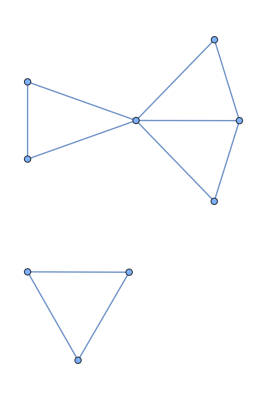
{{False,False,-Graphics-,{1,6},1},{False,False,-Graphics-,{2,0,0},2}}

```mathematica
{DSphereQ[#],DGraphQ[#],DGraphBoundary[#],CountHoles[#],CountHoles[#,1]}&/@{g,GraphFromCliques[fstLst]}
```

CombinatorialManifoldQ, CombinatorialSphereQ, CombinatorialBoundary

```mathematica
CombinatorialManifoldQ[#]&/@{{{1,2,3,4}},{{1}},{},{{1},{2}},{{1},{2},{3}},{{1,2},{2,3},{3,1}}}
CombinatorialSphereQ[#]&/@{{{1,2,3,4}},{{1}},{},{{1},{2}},{{1},{2},{3}},{{1,2},{2,3},{3,1}}}
```

{True,True,True,True,False,True}

{False,False,True,True,False,True}

```mathematica
CombinatorialBoundary[{{1,2,3,4}}]
CombinatorialBoundary[%]
```

{{1,2,3},{1,2,4},{1,3,4},{2,3,4}}

{}

OrientableCombinatorialManifoldQ

```mathematica
mobiusStrip1={{1,2,3},{2,3,4},{3,4,5},{4,5,1},{5,1,2}};
mobiusStrip2={{1,2,3},{2,3,5},{3,4,5},{4,5,6},{2,4,6},{1,2,6}};
kleinbottle={{1,2,5},{2,5,6},{2,3,6},{3,6,7},{1,3,7},{1,5,7},{4,5,6},{4,6,8},{6,7,8},{7,8,9},{5,7,9},{4,5,9},{1,4,8},{1,3,8},{3,8,9},{2,3,9},{2,4,9},{1,2,4}};(*{{0,1,4},{1,4,5},{1,2,5},{2,5,6},{0,2,6},{0,4,6},{3,4,5},{3,5,7},{5,6,7},{6,7,8},{4,6,8},{3,4,8},{0,3,7},{0,2,7},{2,7,8},{1,2,8},{1,3,8},{0,1,3}}+1*)
projectivePlane={{1,2,3},{1,2,5},{1,3,4},{1,4,6},{1,5,6},{2,3,6},{2,4,5},{2,4,6},{3,4,5},{3,5,6}};(*{{0,1,2},{0,1,4},{0,2,3},{0,3,5},{0,4,5},{1,2,5},{1,3,4},{1,3,5},{2,3,4},{2,4,5}}+1*)
torus={{13,15,16},{7,13,15},{14,15,16},{10,14,16},{3,10,14},{10,12,16},{5,10,12},{11,12,16},{11,13,16},{2,11,13},{7,9,15},{5,9,12},{8,14,15},{8,9,15},{5,8,9},{2,5,8},{6,11,12},{6,9,12},{6,7,9},{3,6,7},{4,8,14},{4,6,11},{3,4,14},{3,4,6},{2,4,11},{2,4,8},{1,5,10},{1,7,13},{1,3,10},{1,3,7},{1,2,13},{1,2,5}};
tetrahedron={{1,2,3},{1,2,4},{1,3,4},{2,3,4}};
octahedron={{1,2,3},{1,2,4},{1,3,5},{1,4,5},{6,2,3},{6,2,4},{6,3,5},{6,4,5}};
```

```mathematica
OrientableCombinatorialManifoldQ[#]&/@{mobiusStrip1,mobiusStrip2,kleinbottle,projectivePlane,torus,tetrahedron,octahedron}
```

{False,False,False,False,True,True,True}

```mathematica
Visualize2DComplex[#]&/@{mobiusStrip1,mobiusStrip2,kleinbottle,projectivePlane,torus,tetrahedron,octahedron}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Counting Pure Complexes

RankComb, UnrankComb, NumPureComplexes

```mathematica
UnrankComb[RankComb[{0,1,2},5],5,3]
```

{0,1,2}

```mathematica
NumPureComplexes[3,3]
```

2649

## Choosing Isomorphism Classes

### Graph Isomorphism Classes

```mathematica
rglst=Table[RandomGraph[With[{n=RandomInteger[{4,10}]},{n,RandomInteger[{0,n(n-1)/2}]}]],{10}];
```

```mathematica
GraphPlot[#,ImageSize->{50,50}]&/@rglst
Length[Tally[rglst,IsomorphicGraphQ[#1,#2]&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

10

```mathematica
rAmatlst=Normal[AdjacencyMatrix[#]]&/@rglst;
Length[rAmatlst]
MatrixForm[#]&/@rAmatlst[[1;;3]]
```

10

{(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 1 | 1 | 0
1 | 0 | 1 | 1
1 | 1 | 0 | 1
0 | 1 | 1 | 0),(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 0 | 0 | 1 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 1 | 0 | 0)}

GraphIsContained

```mathematica
GraphIsContained[rglst,rglst[[1]]]
GraphIsContained[rglst,5]
GraphIsContained[rglst,CompleteGraph[20]]
```

True

GraphIsContained::argerr: Input should be of the form 
	GraphIsContained[glist_List,g_Graph] or GraphIsContained[AmatList_List,Amat_List].

$Failed

False

```mathematica
GraphIsContained[rAmatlst,rAmatlst[[1]]]
GraphIsContained[rAmatlst,5]
GraphIsContained[rAmatlst,Normal[AdjacencyMatrix[CompleteGraph[20]]]]
```

True

GraphIsContained::argerr: Input should be of the form 
	GraphIsContained[glist_List,g_Graph] or GraphIsContained[AmatList_List,Amat_List].

$Failed

False

ChooseNonIsomorphicGraphs

```mathematica
Length@ChooseNonIsomorphicGraphs[rglst]
Length@ChooseNonIsomorphicGraphs[rglst,rglst]
Length@ChooseNonIsomorphicGraphs[{rglst,rglst}]
```

10

10

10

```mathematica
Length@ChooseNonIsomorphicGraphs[rAmatlst]
Length@ChooseNonIsomorphicGraphs[rAmatlst,rAmatlst]
Length@ChooseNonIsomorphicGraphs[{rAmatlst,rAmatlst}]
```

10

10

10

### Clique Complex Isomorphism Classes

```mathematica
rClqXlst=FindClique[#,∞,All]&/@(Table[RandomGraph[With[{n=RandomInteger[{4,15}]},{n,RandomInteger[{0,n(n-1)/2}]}]],{10}]);
Length[rClqXlst];
rClqXlst[[1;;3]]
```

{{{7,9},{1,7},{1,5},{8},{6},{4},{3},{2}},{{2,3},{4},{1}},{{3,6,9,11,13},{3,4,6,9,13},{3,6,7,9,11},{3,5,6,9,11},{3,4,5,6,9},{7,8,11,12},{7,8,10,12},{2,9,11,13},{2,8,11,12},{2,8,10,12},{1,2,8,12},{2,4,10,12},{2,4,9,13},{1,2,4,13},{1,2,4,12},{1,3,4,13},{3,7,8,10},{3,7,8,11},{3,5,8,11},{3,5,8,10},{1,3,5,8},{3,4,5,10},{1,3,4,5}}}

```mathematica
GraphPlot[GraphFromCliques[#],ImageSize->{50,50}]&/@rClqXlst
Length[Tally[rClqXlst,IsomorphicGraphQ[GraphFromCliques[#1],GraphFromCliques[#2]]&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

10

IsContainedClqComp

```mathematica
IsContainedClqComp[rClqXlst,rClqXlst[[1]]]
IsContainedClqComp[rClqXlst,5]
IsContainedClqComp[rClqXlst,{Range[25]}]
```

True

IsContainedClqComp::argerr: Input should be of the form 
	IsContainedClqComp[cList_List,cmpx_List], where cList is a list of list of lists (a list of 
	clique complexes each given as a list of facets), and 
	cmpx is a list of lists (facets).

$Failed

False

ChooseNonIsomorphicClqComplexes

```mathematica
Length@ChooseNonIsomorphicClqComplexes[rClqXlst]
Length@ChooseNonIsomorphicClqComplexes[rClqXlst,rClqXlst]
Length@ChooseNonIsomorphicClqComplexes[{rClqXlst,rClqXlst}]
```

10

10

10

### Simplicial Complex Isomorphism Classes

```mathematica
rClqXlst=FindClique[#,∞,All]&/@(Table[RandomGraph[With[{n=RandomInteger[{4,15}]},{n,RandomInteger[{0,n(n-1)/2}]}]],{10}]);
Length[rClqXlst];
rClqXlst[[1;;3]]
```

{{{2,7,8,9,10,11,12},{2,3,7,8,9,10,12},{1,2,7,8,9,11,12},{1,2,6,8,9,11,12},{1,3,4,6,8,9,12},{1,2,3,7,8,9,12},{1,2,3,6,8,9,12},{5,7,9,10,11,12},{3,4,8,9,10,12},{3,4,5,9,10,12},{3,5,7,9,10,12},{1,5,7,9,11,12},{1,3,5,7,9,12},{1,3,4,5,9,12}},{{2,6},{3,8},{3,7},{1,3},{5},{4}},{{2,4},{1,2},{3}}}

```mathematica
GraphPlot[GraphFromCliques[#],ImageSize->{50,50}]&/@rClqXlst
Length[Tally[rClqXlst,IsomorphicGraphQ[GraphFromCliques[#1],GraphFromCliques[#2]]&]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

10

IsomorphicSimplicialComplexQ

```mathematica
IsomorphicSimplicialComplexQ[rClqXlst[[1]],rClqXlst[[1]]]
IsomorphicSimplicialComplexQ[rClqXlst[[1]],rClqXlst[[2]]]
IsomorphicSimplicialComplexQ[rClqXlst[[1]],5]
```

True

False

IsomorphicSimplicialComplexQ::argerr: Input should be of the form 
	IsomorphicSimplicialComplexQ[c1_List, c2_List], where c1 and c2 are each a list of list (the list
	of facets of the complexes).

$Failed

IsContainedSimplicialComp

```mathematica
IsContainedSimplicialComp[rClqXlst,rClqXlst[[1]]]
IsContainedSimplicialComp[rClqXlst,5]
IsContainedSimplicialComp[rClqXlst,{Range[25]}]
```

True

IsContainedSimplicialComp::argerr: Input should be of the form 
	IsContainedSimplicialComp[xList_List, cmpx_List], where xList is a list of list of lists 
	(a list of simplicial complexes each given as a list of facets), and 
	cmpx is a list of lists (facets).

$Failed

False

ChooseNonIsomorphicSimplicialComplexes

```mathematica
Length@ChooseNonIsomorphicSimplicialComplexes[rClqXlst]
Length@ChooseNonIsomorphicSimplicialComplexes[rClqXlst,rClqXlst]
Length@ChooseNonIsomorphicSimplicialComplexes[{rClqXlst,rClqXlst}]
```

10

10

10

## Automorphism Groups and Orders

### Simplicial Complex Automorphism and Facet Automorphism

SimplicialComplexAutomorphismGroupOrder

```mathematica
g=-Graphics-;
fstLst={{1,2,3},{3,5,6},{3,5,7},{4,9,10}};
GraphPlot[#,VertexLabels->Automatic]&/@{g,GraphFromCliques[fstLst]}
```

{-Graphics-,-Graphics-}

```mathematica
SimplicialComplexAutomorphismGroupOrder[fstLst]
```

24

```mathematica
IsomorphicSimplicialComplexQ[{{1,2,3},{3,5,6},{3,5,7}},{{4,9,10}}]
```

False

PureComplexAutomorphismGroup

PureComplexAutomorphismGroupOrder

PureComplexFacetStabilizerGroupOrder

PureComplexFacetAutomorphismGroupOrder

PureComplexFacetAutomorphismGroup

### Clique Complex Automorphism and Facet Automorphism

CliqueFacetStabilixerGroupOrder

CliqueFacetAutomorphismGroupOrder

CliqueFacetAutomorphismGroup

## Generate Pure Simplicial Complexes

## Generate All Pure Simplicial Complexes

### Generate all vertex labeled pure simplicial complexes

GenerateAllVertexLabeledPureSimplicialComplexes

```mathematica
GenerateAllVertexLabeledPureSimplicialComplexes[{2,2,3}]
```

{{{1,2},{1,3}},{{1,2},{2,3}},{{1,3},{2,3}}}

```mathematica
GenerateAllVertexLabeledPureSimplicialComplexes[{2,2}]
```

{{{1,2},{1,3}},{{1,2},{2,3}},{{1,3},{2,3}},{{1,2},{3,4}},{{1,3},{2,4}},{{1,4},{2,3}}}

### Generate all facet-labeled pure simplicial complexes

GenerateAllFacetLabeledPureSimplicialComplexes

```mathematica
flabeledSXs=GenerateAllFacetLabeledPureSimplicialComplexes[{2,2}]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->{75,75}]&/@flabeledSXs
```

{{{1,2},{1,3}},{{1,2},{3,4}}}

{-Graphics-,-Graphics-}

```mathematica
(FacetLabeledVertexListFromComplex[#]&/@flabeledSXs)
ComplexFromFacetLabeledVertexList[#]&/@%
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->{60,60}]&/@%
```

{{{1,2},{1},{2}},{{1},{1},{2},{2}}}

{{{1,2},{1,3}},{{1,2},{3,4}}}

{-Graphics-,-Graphics-}

```mathematica
vlabeledSXs=GenerateAllVertexLabeledPureSimplicialComplexes[{2,4}]
Length[vlabeledSXs];
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->{60,60}]&/@vlabeledSXs[[1;;3]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
gr=GroupBy[vlabeledSXs,(FacetLabeledVertexListFromComplex[#])&]
```

```mathematica
<|Table[i->ComplexFromFacetLabeledVertexList[i],{i,Keys[gr]}]|>
```

<|{{1,3,4},{2,3},{2,4},{1}}→{{1,2},{1,3},{1,4},{2,3}},{{1,2,3},{1,4},{2,4},{3}}→{{1,2},{1,3},{1,4},{2,3}},{{1,2,3},{1,4},{3,4},{2}}→{{1,2},{1,3},{1,4},{2,3}},{{1,2,3},{2,4},{3,4},{1}}→{{1,2},{1,3},{1,4},{2,3}},{{1,2},{1,3},{2,4},{3,4}}→{{1,2},{1,3},{2,4},{3,4}},{{1,3,4},{1,2},{2,4},{3}}→{{1,2},{1,3},{1,4},{2,3}},{{2,3,4},{1,2},{1,4},{3}}→{{1,2},{1,3},{1,4},{2,3}},{{1,2,4},{2,3},{3,4},{1}}→{{1,2},{1,3},{1,4},{2,3}},{{1,3,4},{1,2},{2,3},{4}}→{{1,2},{1,3},{1,4},{2,3}},{{2,3,4},{1,2},{1,3},{4}}→{{1,2},{1,3},{1,4},{2,3}},{{2,3},{2,4},{3,4},{1},{1}}→{{1,2},{1,3},{2,3},{4,5}},{{1,4},{2,3},{2,4},{1},{3}}→{{1,3},{1,4},{2,3},{2,5}},{{1,4},{2,3},{3,4},{1},{2}}→{{1,3},{1,4},{2,3},{2,5}},{{1,3},{2,4},{3,4},{1},{2}}→{{1,3},{1,4},{2,3},{2,5}},{{1,3,4},{2,4},{1},{2},{3}}→{{1,2},{1,3},{1,5},{2,4}},{{2,3,4},{1,4},{1},{2},{3}}→{{1,2},{1,4},{1,5},{2,3}},{{1,3,4},{2,3},{1},{2},{4}}→{{1,2},{1,3},{1,5},{2,4}},{{2,3,4},{1,3},{1},{2},{4}}→{{1,2},{1,4},{1,5},{2,3}},{{1,3},{2,3},{2,4},{1},{4}}→{{1,2},{1,4},{2,3},{3,5}},{{1,2},{2,4},{3,4},{1},{3}}→{{1,2},{1,4},{2,3},{3,5}},{{1,2},{1,4},{2,4},{3},{3}}→{{1,2},{1,3},{2,3},{4,5}},{{1,2},{1,4},{3,4},{2},{3}}→{{1,2},{1,4},{2,3},{3,5}},{{1,2,4},{3,4},{1},{2},{3}}→{{1,2},{1,3},{1,4},{2,5}},{{1,2},{1,3},{2,3},{4},{4}}→{{1,2},{1,3},{2,3},{4,5}},{{1,2,3,4},{1},{2},{3},{4}}→{{1,2},{1,3},{1,4},{1,5}},{{1,2,3},{1,4},{2},{3},{4}}→{{1,2},{1,3},{1,4},{2,5}},{{1,2,3},{2,4},{1},{3},{4}}→{{1,2},{1,3},{1,4},{2,5}},{{1,2,3},{3,4},{1},{2},{4}}→{{1,2},{1,3},{1,4},{2,5}},{{1,3,4},{1,2},{2},{3},{4}}→{{1,2},{1,4},{1,5},{2,3}},{{1,2},{1,3},{2,4},{3},{4}}→{{1,2},{1,3},{2,4},{3,5}},{{1,2},{1,3},{3,4},{2},{4}}→{{1,2},{1,4},{2,3},{3,5}},{{2,3,4},{1,2},{1},{3},{4}}→{{1,2},{1,4},{1,5},{2,3}},{{1,2},{2,3},{3,4},{1},{4}}→{{1,2},{1,4},{2,3},{3,5}},{{1,2},{1,4},{2,3},{3},{4}}→{{1,2},{1,3},{2,5},{3,4}},{{1,2,4},{2,3},{1},{3},{4}}→{{1,2},{1,3},{1,5},{2,4}},{{2,4},{3,4},{1},{1},{2},{3}}→{{1,2},{1,5},{2,6},{3,4}},{{1,4},{2,4},{1},{2},{3},{3}}→{{1,2},{1,3},{2,4},{5,6}},{{1,4},{3,4},{1},{2},{2},{3}}→{{1,2},{1,3},{2,6},{4,5}},{{1,3},{2,3},{1},{2},{4},{4}}→{{1,2},{1,3},{2,4},{5,6}},{{2,3,4},{1},{1},{2},{3},{4}}→{{1,4},{1,5},{1,6},{2,3}},{{2,3},{2,4},{1},{1},{3},{4}}→{{1,2},{1,5},{2,6},{3,4}},{{2,3},{3,4},{1},{1},{2},{4}}→{{1,2},{1,5},{2,6},{3,4}},{{1,4},{2,3},{1},{2},{3},{4}}→{{1,3},{1,6},{2,4},{2,5}},{{1,3,4},{1},{2},{2},{3},{4}}→{{1,2},{1,5},{1,6},{3,4}},{{1,3},{2,4},{1},{2},{3},{4}}→{{1,3},{1,5},{2,4},{2,6}},{{1,3},{3,4},{1},{2},{2},{4}}→{{1,2},{1,3},{2,6},{4,5}},{{1,2},{3,4},{1},{2},{3},{4}}→{{1,3},{1,4},{2,5},{2,6}},{{1,2},{2,4},{1},{3},{3},{4}}→{{1,2},{1,3},{2,6},{4,5}},{{1,2},{1,4},{2},{3},{3},{4}}→{{1,2},{1,3},{2,6},{4,5}},{{1,2,4},{1},{2},{3},{3},{4}}→{{1,2},{1,3},{1,6},{4,5}},{{1,2,3},{1},{2},{3},{4},{4}}→{{1,2},{1,3},{1,4},{5,6}},{{1,2},{1,3},{2},{3},{4},{4}}→{{1,2},{1,3},{2,4},{5,6}},{{1,2},{2,3},{1},{3},{4},{4}}→{{1,2},{1,3},{2,4},{5,6}},{{3,4},{1},{1},{2},{2},{3},{4}}→{{1,6},{1,7},{2,3},{4,5}},{{2,4},{1},{1},{2},{3},{3},{4}}→{{1,4},{1,7},{2,3},{5,6}},{{1,4},{1},{2},{2},{3},{3},{4}}→{{1,2},{1,7},{3,4},{5,6}},{{2,3},{1},{1},{2},{3},{4},{4}}→{{1,4},{1,5},{2,3},{6,7}},{{1,3},{1},{2},{2},{3},{4},{4}}→{{1,2},{1,5},{3,4},{6,7}},{{1,2},{1},{2},{3},{3},{4},{4}}→{{1,2},{1,3},{4,5},{6,7}},{{1},{1},{2},{2},{3},{3},{4},{4}}→{{1,2},{3,4},{5,6},{7,8}}|>

```mathematica
KeySortBy[Length/@Map[GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->{80,80}]&,gr,{2}],Length/@#&]
(*Length/@%*)
```

<|{{1,2},{1,3},{2,4},{3,4}}→3,{{1,2,3},{1,4},{2,4},{3}}→1,{{1,2,3},{1,4},{3,4},{2}}→1,{{1,2,3},{2,4},{3,4},{1}}→2,{{1,2,4},{2,3},{3,4},{1}}→1,{{1,3,4},{1,2},{2,3},{4}}→1,{{1,3,4},{1,2},{2,4},{3}}→2,{{1,3,4},{2,3},{2,4},{1}}→1,{{2,3,4},{1,2},{1,3},{4}}→2,{{2,3,4},{1,2},{1,4},{3}}→1,{{1,2},{1,3},{2,3},{4},{4}}→3,{{1,2},{1,3},{2,4},{3},{4}}→9,{{1,2},{1,3},{3,4},{2},{4}}→8,{{1,2},{1,4},{2,3},{3},{4}}→3,{{1,2},{1,4},{2,4},{3},{3}}→3,{{1,2},{1,4},{3,4},{2},{3}}→4,{{1,2},{2,3},{3,4},{1},{4}}→10,{{1,2},{2,4},{3,4},{1},{3}}→11,{{1,3},{2,3},{2,4},{1},{4}}→3,{{1,3},{2,4},{3,4},{1},{2}}→3,{{1,4},{2,3},{2,4},{1},{3}}→3,{{1,4},{2,3},{3,4},{1},{2}}→6,{{2,3},{2,4},{3,4},{1},{1}}→4,{{1,2,3},{1,4},{2},{3},{4}}→4,{{1,2,3},{2,4},{1},{3},{4}}→7,{{1,2,3},{3,4},{1},{2},{4}}→10,{{1,2,4},{2,3},{1},{3},{4}}→3,{{1,2,4},{3,4},{1},{2},{3}}→3,{{1,3,4},{1,2},{2},{3},{4}}→6,{{1,3,4},{2,3},{1},{2},{4}}→6,{{1,3,4},{2,4},{1},{2},{3}}→3,{{2,3,4},{1,2},{1},{3},{4}}→10,{{2,3,4},{1,3},{1},{2},{4}}→4,{{2,3,4},{1,4},{1},{2},{3}}→4,{{1,2,3,4},{1},{2},{3},{4}}→5,{{1,2},{1,3},{2},{3},{4},{4}}→18,{{1,2},{1,4},{2},{3},{3},{4}}→12,{{1,2},{2,3},{1},{3},{4},{4}}→24,{{1,2},{2,4},{1},{3},{3},{4}}→24,{{1,2},{3,4},{1},{2},{3},{4}}→54,{{1,3},{2,3},{1},{2},{4},{4}}→12,{{1,3},{2,4},{1},{2},{3},{4}}→12,{{1,3},{3,4},{1},{2},{2},{4}}→12,{{1,4},{2,3},{1},{2},{3},{4}}→24,{{1,4},{2,4},{1},{2},{3},{3}}→6,{{1,4},{3,4},{1},{2},{2},{3}}→12,{{2,3},{2,4},{1},{1},{3},{4}}→15,{{2,3},{3,4},{1},{1},{2},{4}}→30,{{2,4},{3,4},{1},{1},{2},{3}}→15,{{1,2,3},{1},{2},{3},{4},{4}}→22,{{1,2,4},{1},{2},{3},{3},{4}}→6,{{1,3,4},{1},{2},{2},{3},{4}}→12,{{2,3,4},{1},{1},{2},{3},{4}}→20,{{1,2},{1},{2},{3},{3},{4},{4}}→75,{{1,3},{1},{2},{2},{3},{4},{4}}→30,{{1,4},{1},{2},{2},{3},{3},{4}}→30,{{2,3},{1},{1},{2},{3},{4},{4}}→72,{{2,4},{1},{1},{2},{3},{3},{4}}→36,{{3,4},{1},{1},{2},{2},{3},{4}}→72,{{1},{1},{2},{2},{3},{3},{4},{4}}→105|>

```mathematica
FacetLabeledVertexListFromComplex[#]&/@vlabeledSXs
```

{{{1,3},{2,3},{1},{2}},{{1,3},{2,3},{1},{2}},{{1,3},{2,3},{1},{2}},{{1,2,3},{1},{2},{3}},{{1,2},{1,3},{2},{3}},{{1,2},{2,3},{1},{3}},{{1,2},{1,3},{2},{3}},{{1,2},{2,3},{1},{3}},{{1,2,3},{1},{2},{3}},{{1,2},{2,3},{1},{3}},{{1,2},{2,3},{1},{3}},{{1,2},{1,3},{2},{3}},{{1,2},{2,3},{1},{3}},{{1,2},{2,3},{1},{3}},{{1,2,3},{1},{2},{3}},{{1,2,3},{1},{2},{3}}}

## Generate A Random Pure Simplicial Complex

### Random [purity*facetOrder]-labeled Pure Simplicial Complex

RandomPQLabeledPureSimplicialComplex

{{1,2},{2,3}}

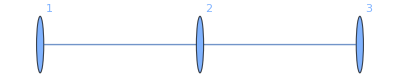

```mathematica
RandomPQLabeledPureSimplicialComplex[{2,2}]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&@%
```

{{{1,2},{2,4}},{{1,2},{1,3},{1,4},{2,4}},{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},{{1,2},{1,2},{1,3},{1,3},{1,4},{2,3},{2,4},{3,4}}}

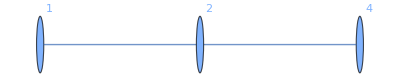
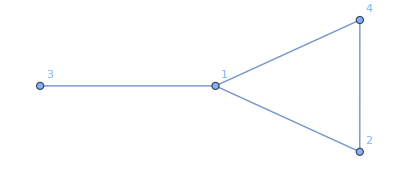
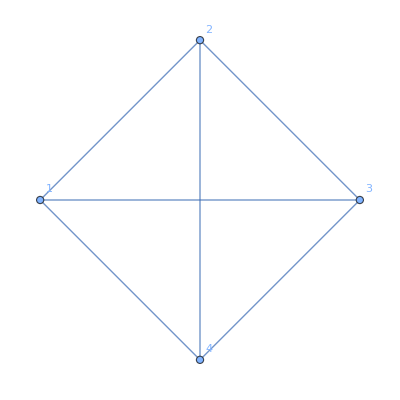
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomPQLabeledPureSimplicialComplex[{2,2},4]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&/@%
```

### Random Vertex labeled Pure Simplicial Complex

RandomVertexLabeledPureSimplicialComplex

{{1,4},{2,3},{2,4}}

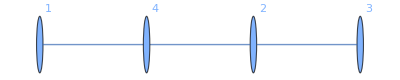

```mathematica
RandomVertexLabeledPureSimplicialComplex[{2,3,4}]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&@%
```

{{{3,4},{1,2},{1,4}},{{1,2},{1,3},{3,4}},{{2,4},{3,4},{1,4}},{{2,4},{1,2},{3,4}},{{1,4},{2,3},{1,2}},{{1,4},{2,4},{1,3}},{{2,3},{1,4},{1,3}},{{2,4},{2,3},{1,2}},{{3,4},{2,3},{1,2}},{{1,4},{2,3},{1,2}}}

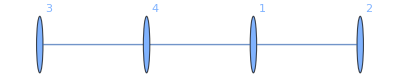
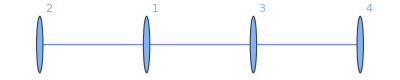
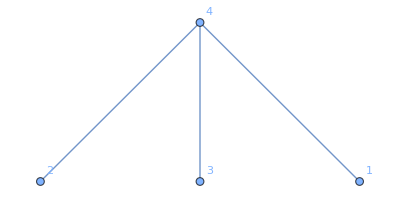
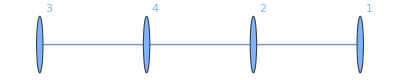
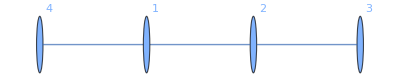
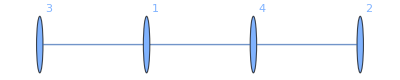
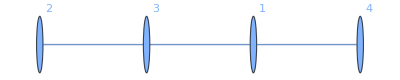
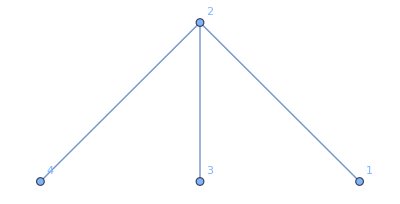
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomVertexLabeledPureSimplicialComplex[{2,3,4},10]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&/@%
```

{{3,5},{2,4},{1,6}}

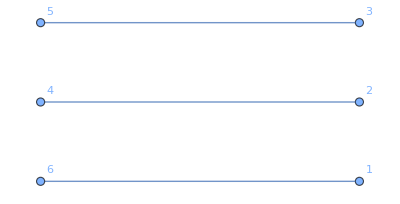

```mathematica
RandomVertexLabeledPureSimplicialComplex[{2,3}]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&@%
```

{{{2,4},{1,2},{2,3}},{{1,2},{3,4},{1,5}},{{2,4},{1,5},{1,3}},{{2,3},{2,5},{1,4}},{{1,3},{2,6},{4,5}},{{1,4},{2,3},{3,5}}}

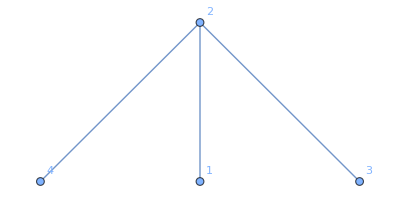
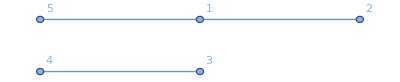
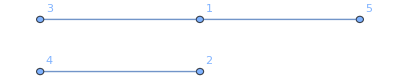
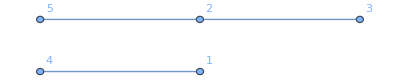
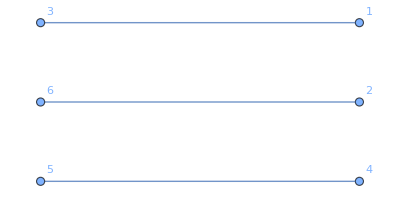
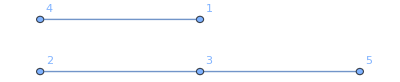

```mathematica
RandomVertexLabeledPureSimplicialComplex[{2,3},6]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&/@%
```

### Random facet labeled Pure Simplicial Complex

RandomFacetLabeledPureSimplicialComplex

{{1,3},{2,4},{3,4}}

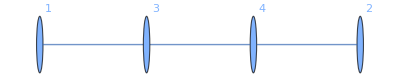

```mathematica
RandomFacetLabeledPureSimplicialComplex[{2,3}]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&@%
```

{{{1,4},{2,4},{3,4}},{{1,5},{2,5},{3,4}},{{1,2},{1,3},{2,3}},{{1,3},{2,4},{3,4}},{{1,2},{3,4},{5,6}},{{1,4},{2,4},{3,4}},{{1,5},{2,3},{4,5}},{{1,5},{2,5},{3,4}},{{1,5},{2,3},{4,5}},{{1,4},{2,4},{3,4}}}

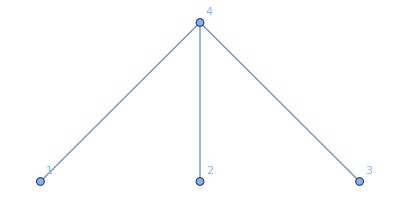
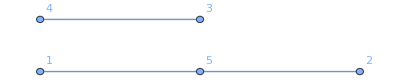
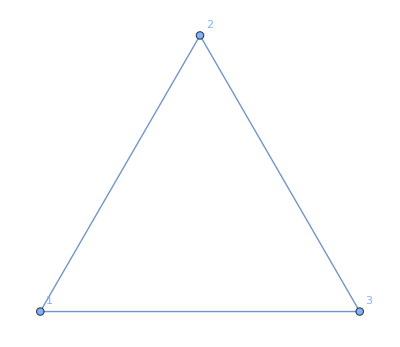
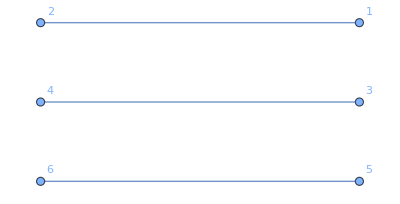
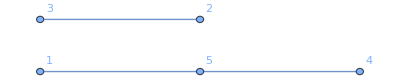
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RandomFacetLabeledPureSimplicialComplex[{2,3},10]
GraphPlot[GraphFromCliques[#],VertexLabels->Automatic,ImageSize->Tiny]&/@%
```